{Ωc 1/2+ 2.695}

{2.68222,4.91384,{3.07914,2.95499,2.48281,2.04279}}

{0.27916}

{{-0.404814},{-0.383436},{-1.07088}}

{Ωc^* 3/2+ 2.766}

{2.7667,5.08144,{3.08118,2.96069,2.49254,2.04279}}

{0.287883}

{{-0.33814},{-0.320283},{-0.894503}}

{Ds 0- 1.968}

{1.95938,3.73718,{3.05977,2.90268,2.40716,2.04279}}

{0.456295,0.456295}

{Ds^* 1- 2.112}

{2.11225,4.14369,{3.06768,2.92365,2.43484,2.04279}}

{0.502059,0.502059}

{{0.407954,-0.407954},{0.38641,-0.38641},{1.07918,-1.07918}}

{Ωb 1/2+ 6.046}

{6.08483,4.74206,{3.0769,2.94878,2.47259,2.04279}}

{0.592263}

{{-0.322685},{-0.305644},{-0.853618}}

{Ωb^* 3/2+}

{6.11717,4.81997,{3.07794,2.95165,2.47726,2.04279}}

{0.601409}

{{-0.538698},{-0.51025},{-1.42505}}

{Bs 0- 5.367}

{5.34461,3.28669,{3.04878,2.8745,2.37437,2.04279}}

{0.155154,0.155154}

{Bs^* 1- 5.415}

{5.41529,3.56637,{3.05592,2.89269,2.395,2.04279}}

{0.167088,0.167088}

{{0.377161,-0.377161},{0.357244,-0.357244},{0.997727,-0.997727}}

{ηc 0- 2.984}

{2.99497,3.02678,{3.041,2.85522,2.35435,2.04279}}

{0.}

{Jψ 1- 3.097}

{3.09707,3.43774,{3.05278,2.88462,2.38562,2.04279}}

{0.}

{{0.},{0.},{0.}}

{Bc 0- 6.275}

{6.26353,2.33279,{3.01214,2.78841,2.29658,2.04279}}

{0.27317,0.27317}

{Bc^* 1-}

{6.33186,2.6378,{3.02661,2.82099,2.32278,2.04279}}

{0.305686,0.305686}

{{0.194505,-0.194505},{0.184233,-0.184233},{0.514535,-0.514535}}

{ηb 0- 9.399}

{9.38091,1.4321,{2.93703,2.64556,2.21084,2.04279}}

{0.}

{Υ 1- 9.460}

{9.46043,1.63228,{2.96018,2.68534,2.23106,2.04279}}

{0.}

{{0.},{0.},{0.}}

{Ξcc 1/2+ 3.621}

{3.60914,4.38662,{3.07172,2.93457,2.45058,2.04279}}

{0.772697,0.445863}

{{0.0482363,0.344035},{0.045689,0.325867},{0.127602,0.910096}}

{Ξcc^* 3/2+ 1.533}

{3.72026,4.60706,{3.07503,2.94361,2.46437,2.04279}}

{0.809853,0.465363}

{{0.992396,0.0604068},{0.939988,0.0572168},{2.62524,0.159798}}

{Ξbb 1/2+}

{10.342,3.63493,{3.05751,2.89679,2.39992,2.04279}}

{0.28162,0.440632}

{{-0.206275,0.0388351},{-0.195382,0.0367842},{-0.545672,0.102733}}

{Ξbb^* 3/2+}

{10.3921,3.80006,{3.0611,2.90617,2.41156,2.04279}}

{0.294946,0.46031}

{{0.448096,-0.320641},{0.424433,-0.303708},{1.18538,-0.848209}}

{Mass Spectrum}

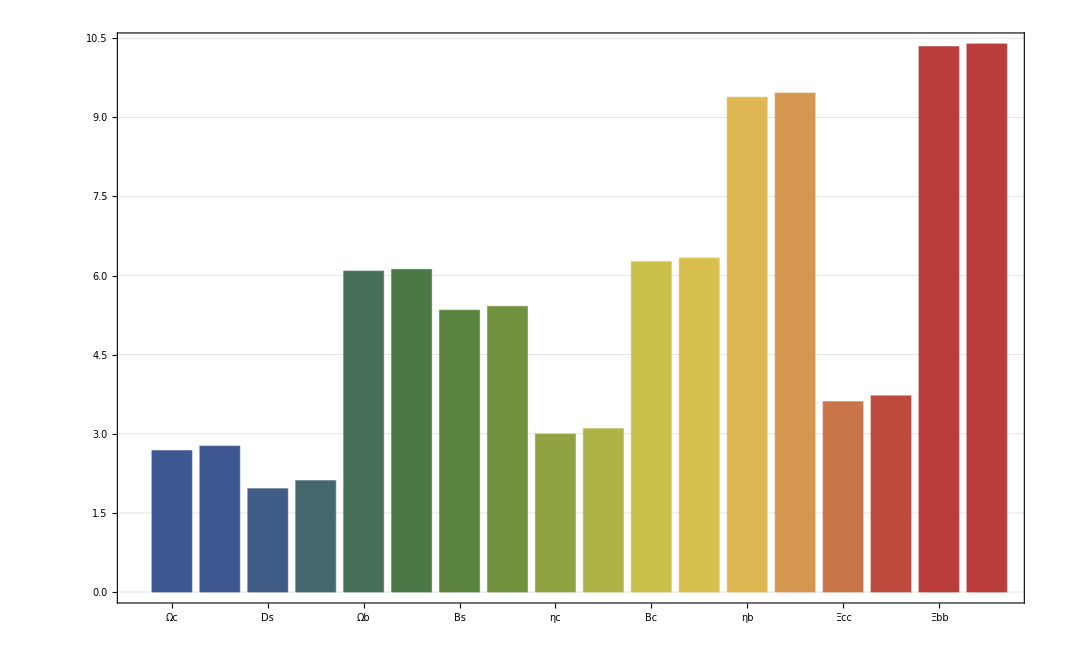

{My Error}

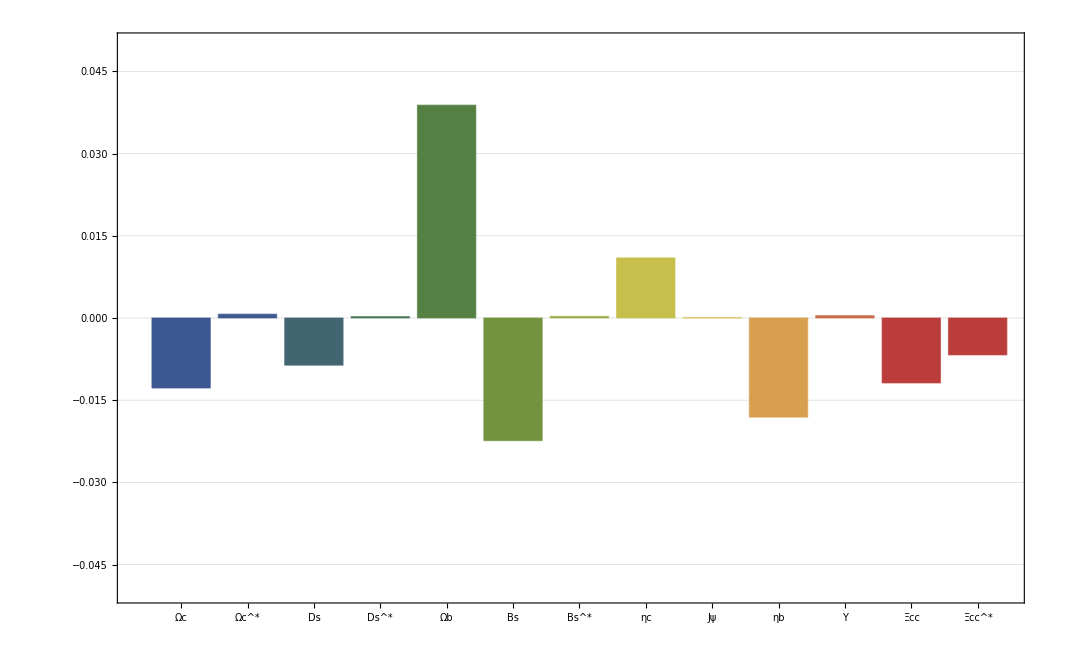

{Charge Radius}

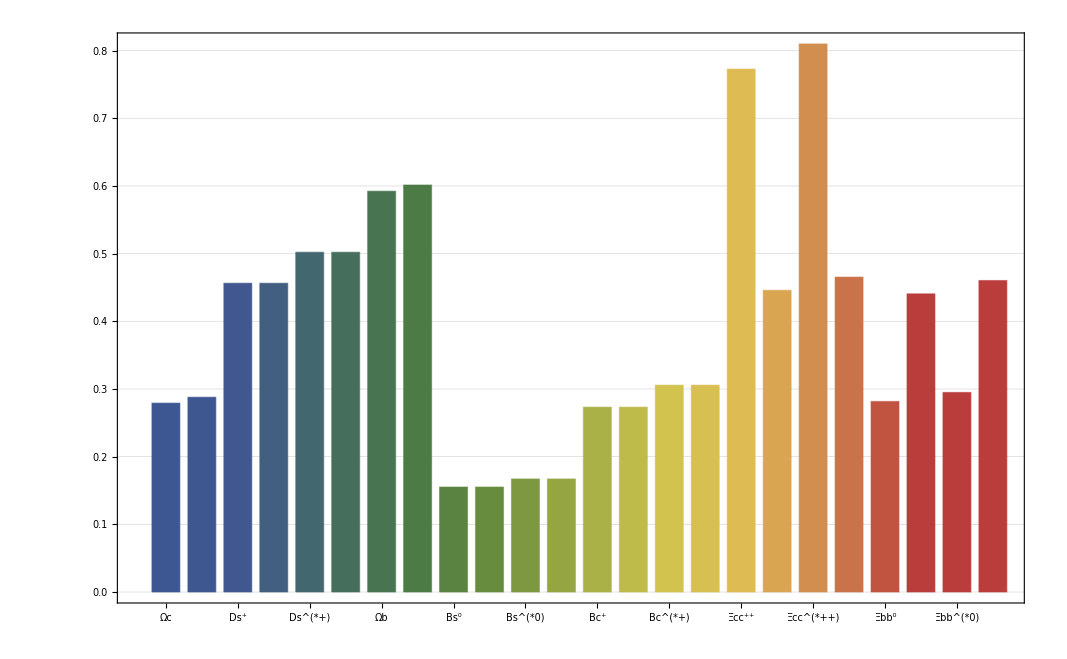

{Magnetic Moment}

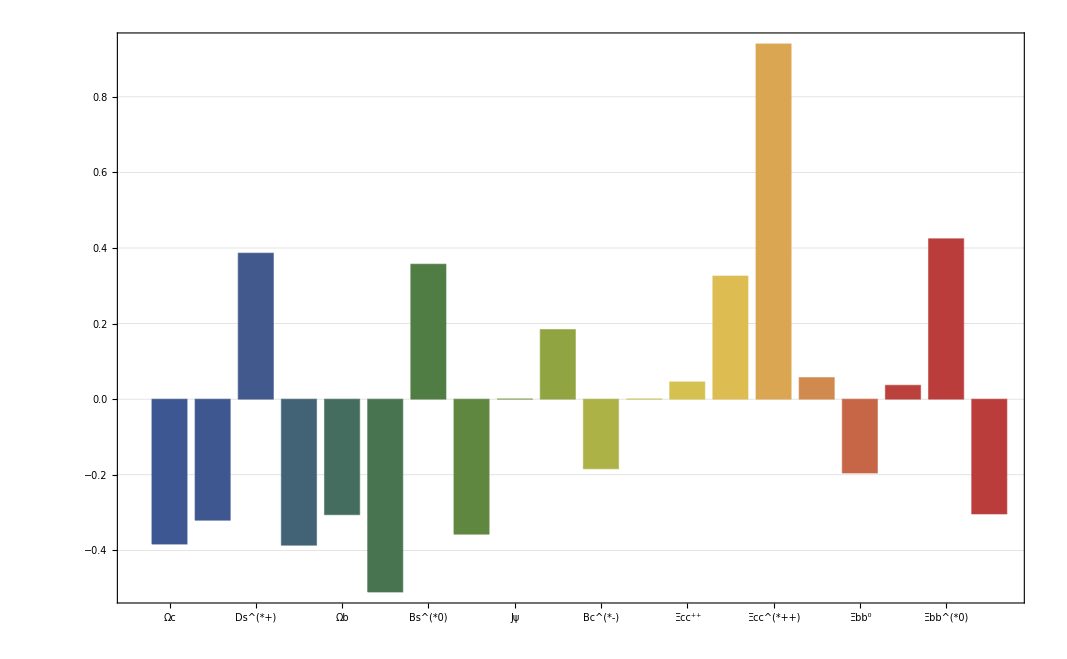

```mathematica
<<MITBagModel/MITBagModel.m

Nc=Hadron[{0,0,0,3},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}];
μNp=MagneticMoment[{0,0,0,4/3,-1/3},{0,0,0,0,0},Nc];
γμN=2.7928473446;

{"Ωc 1/2+ 2.695"}
Ωc=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,32/3,0},{0,0,-8/3,0},{0,0,0,0}},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}}]
rΩc=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},Ωc];
μΩc=MagneticMoment[{0,-1/3,4/3,0,0},{0,0,0,0,0},Ωc];
{rΩc}
{{μΩc},{μΩc/μNp},γμN{μΩc/μNp}}

{"Ωc^* 3/2+ 2.766"}
ΩcStar=Hadron[{0,1,2,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,-8/3,0},{0,0,0,0}},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}}]
rΩcStar=ChargeRadius[{0,1,2,0,0},{0,0,0,0,0},ΩcStar];
μΩcStar=MagneticMoment[{0,1,2,0,0},{0,0,0,0,0},ΩcStar];
{rΩcStar}
{{μΩcStar},{μΩcStar/μNp},γμN{μΩcStar/μNp}}

{"Ds 0- 1.968"}
Ds=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,16,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}}]
rDsp=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},Ds];
rDsm=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},Ds];
{rDsp,rDsm}

{"Ds^* 1- 2.112"}
DsStar=Hadron[{0,1,1,0},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,-16/3,0},{0,0,0,0},{0,0,0,0}}]
rDspStar=ChargeRadius[{0,1,0,0,0},{0,0,1,0,0},DsStar];
rDsmStar=ChargeRadius[{0,0,1,0,0},{0,1,0,0,0},DsStar];
μDspStar=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},DsStar];
μDsmStar=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},DsStar];
{rDspStar,rDsmStar}
{{μDspStar,μDsmStar},{μDspStar/μNp,μDsmStar/μNp},γμN{μDspStar/μNp,μDsmStar/μNp}}

{"Ωb 1/2+ 6.046"}
Ωb=Hadron[{1,0,2,0},{{0,0,32/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΩb=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},Ωb];
μΩb=MagneticMoment[{-1/3,0,4/3,0,0},{0,0,0,0,0},Ωb];
{rΩb}
{{μΩb},{μΩb/μNp},γμN{μΩb/μNp}}

{"Ωb^* 3/2+"}
ΩbStar=Hadron[{1,0,2,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,-8/3,0},{0,0,0,0}},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΩbStar=ChargeRadius[{1,0,2,0,0},{0,0,0,0,0},ΩbStar];
μΩbStar=MagneticMoment[{1,0,2,0,0},{0,0,0,0,0},ΩbStar];
{rΩbStar}
{{μΩbStar},{μΩbStar/μNp},γμN{μΩbStar/μNp}}

{"Bs 0- 5.367"}
Bs=Hadron[{1,0,1,0},{{0,0,16,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rBs0=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},Bs];
rBs0bar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},Bs];
{rBs0,rBs0bar}

{"Bs^* 1- 5.415"}
BsStar=Hadron[{1,0,1,0},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,-16/3,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rBs0Star=ChargeRadius[{0,0,1,0,0},{1,0,0,0,0},BsStar];
rBs0barStar=ChargeRadius[{1,0,0,0,0},{0,0,1,0,0},BsStar];
μBs0Star=MagneticMoment[{0,1,0,0,0},{0,0,1,0,0},BsStar];
μBs0barStar=MagneticMoment[{0,0,1,0,0},{0,1,0,0,0},BsStar];
{rBs0Star,rBs0barStar}
{{μBs0Star,μBs0barStar},{μBs0Star/μNp,μBs0barStar/μNp},γμN{μBs0Star/μNp,μBs0barStar/μNp}}

{"ηc 0- 2.984"}
ηc=Hadron[{0,2,0,0},{{0,0,0,0},{0,16,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}}]
rηc=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},ηc];
{rηc}

{"Jψ 1- 3.097"}
Jψ=Hadron[{0,2,0,0},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-16/3,0,0},{0,0,0,0},{0,0,0,0}}]
rJψ=ChargeRadius[{0,1,0,0,0},{0,1,0,0,0},Jψ];
μJψ=MagneticMoment[{0,1,0,0,0},{0,1,0,0,0},Jψ];
{rJψ}
{{μJψ},{μJψ/μNp},γμN{μJψ/μNp}}

{"Bc 0- 6.275"}
Bc=Hadron[{1,1,0,0},{{0,16,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rBcp=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},Bc];
rBcm=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},Bc];
{rBcp,rBcm}

{"Bc^* 1-"}
BcStar=Hadron[{1,1,0,0},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-16/3,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rBcpStar=ChargeRadius[{0,1,0,0,0},{1,0,0,0,0},BcStar];
rBcmStar=ChargeRadius[{1,0,0,0,0},{0,1,0,0,0},BcStar];
μBcpStar=MagneticMoment[{0,1,0,0,0},{1,0,0,0,0},BcStar];
μBcmStar=MagneticMoment[{1,0,0,0,0},{0,1,0,0,0},BcStar];
{rBcpStar,rBcmStar}
{{μBcpStar,μBcmStar},{μBcpStar/μNp,μBcmStar/μNp},γμN{μBcpStar/μNp,μBcmStar/μNp}}

{"ηb 0- 9.399"}
ηb=Hadron[{2,0,0,0},{{16,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rηb=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},ηb];
{rηb}

{"Υ 1- 9.460"}
Υ=Hadron[{2,0,0,0},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-16/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΥ=ChargeRadius[{1,0,0,0,0},{1,0,0,0,0},Υ];
μΥ=MagneticMoment[{1,0,0,0,0},{1,0,0,0,0},Υ];
{rΥ}
{{μΥ},{μΥ/μNp},γμN{μΥ/μNp}}

{"Ξcc 1/2+ 3.621"}
Ξcc=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,32/3},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}}]
rΞccpp=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},Ξcc];
rΞccp=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},Ξcc];
μΞccpp=MagneticMoment[{0,4/3,0,-1/3,0},{0,0,0,0,0},Ξcc];
μΞccp=MagneticMoment[{0,4/3,0,0,-1/3},{0,0,0,0,0},Ξcc];
{rΞccpp,rΞccp}
{{μΞccpp,μΞccp},{μΞccpp/μNp,μΞccp/μNp},γμN{μΞccpp/μNp,μΞccp/μNp}}

{"Ξcc^* 3/2+ 1.533"}
ΞccStar=Hadron[{0,2,0,1},{{0,0,0,0},{0,-8/3,0,-16/3},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,-8/3,0,0},{0,0,0,0},{0,0,0,0}}]
rΞccppStar=ChargeRadius[{0,2,0,1,0},{0,0,0,0,0},ΞccStar];
rΞccpStar=ChargeRadius[{0,2,0,0,1},{0,0,0,0,0},ΞccStar];
μΞccppStar=MagneticMoment[{0,2,0,1,0},{0,0,0,0,0},ΞccStar];
μΞccpStar=MagneticMoment[{0,2,0,0,1},{0,0,0,0,0},ΞccStar];
{rΞccppStar,rΞccpStar}
{{μΞccppStar,μΞccpStar},{μΞccppStar/μNp,μΞccpStar/μNp},γμN{μΞccppStar/μNp,μΞccpStar/μNp}}

{"Ξbb 1/2+"}
Ξbb=Hadron[{2,0,0,1},{{-8/3,0,0,32/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-8/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΞbb0=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},Ξbb];
rΞbbm=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},Ξbb];
μΞbb0=MagneticMoment[{4/3,0,0,-1/3,0},{0,0,0,0,0},Ξbb];
μΞbbm=MagneticMoment[{4/3,0,0,0,-1/3},{0,0,0,0,0},Ξbb];
{rΞbb0,rΞbbm}
{{μΞbb0,μΞbbm},{μΞbb0/μNp,μΞbbm/μNp},γμN{μΞbb0/μNp,μΞbbm/μNp}}

{"Ξbb^* 3/2+"}
ΞbbStar=Hadron[{2,0,0,1},{{-8/3,0,0,-16/3},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{-8/3,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
rΞbb0Star=ChargeRadius[{2,0,0,1,0},{0,0,0,0,0},ΞbbStar];
rΞbbmStar=ChargeRadius[{2,0,0,0,1},{0,0,0,0,0},ΞbbStar];
μΞbb0Star=MagneticMoment[{2,0,0,1,0},{0,0,0,0,0},ΞbbStar];
μΞbbmStar=MagneticMoment[{2,0,0,0,1},{0,0,0,0,0},ΞbbStar];
{rΞbb0Star,rΞbbmStar}
{{μΞbb0Star,μΞbbmStar},{μΞbb0Star/μNp,μΞbbmStar/μNp},γμN{μΞbb0Star/μNp,μΞbbmStar/μNp}}


{"Mass Spectrum"}
BarChart[{First[Ωc],First[ΩcStar],First[Ds],First[DsStar],First[Ωb],First[ΩbStar],First[Bs],First[BsStar],First[ηc],First[Jψ],First[Bc],First[BcStar],First[ηb],First[Υ],First[Ξcc],First[ΞccStar],First[Ξbb],First[ΞbbStar]},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Ωb^*","Bs","Bs^*","ηc","Jψ","Bc","Bc^*","ηb","Υ","Ξcc","Ξcc^*","Ξbb","Ξbb^*"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"My Error"}
BarChart[{
(First[Ωc]-2.695),
(First[ΩcStar]-2.766),
(First[Ds]-1.968),
(First[DsStar]-2.112),
(First[Ωb]-6.046),
(First[Bs]-5.367),
(First[BsStar]-5.415),
(First[ηc]-2.984),
(First[Jψ]-3.097),
(First[ηb]-9.399),
(First[Υ]-9.460),
(First[Ξcc]-3.621),
(First[ΞccStar]-3.727)},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds","Ds^*","Ωb","Bs","Bs^*","ηc","Jψ","ηb","Υ","Ξcc","Ξcc^*"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.05},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Charge Radius"}
BarChart[{rΩc,rΩcStar,rDsp,rDsm,rDspStar,rDsmStar,rΩb,rΩbStar,rBs0,rBs0bar,rBs0Star,rBs0barStar,rBcp,rBcm,rBcpStar,rBcmStar,rΞccpp,rΞccp,rΞccppStar,rΞccpStar,rΞbb0,rΞbbm,rΞbb0Star,rΞbbmStar},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^+","Ds^-","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^0","OverBar[Bs]^0","Bs^(*0)","OverBar[Bs]^(*0)","Bc^+","Bc^-","Bc^(*+)","Bc^(*-)","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]

{"Magnetic Moment"}
BarChart[{μΩc/μNp,μΩcStar/μNp,μDspStar/μNp,μDsmStar/μNp,μΩb/μNp,μΩbStar/μNp,μBs0Star/μNp,μBs0barStar/μNp,μJψ/μNp,μBcpStar/μNp,μBcmStar/μNp,μΥ/μNp,μΞccpp/μNp,μΞccp/μNp,μΞccppStar/μNp,μΞccpStar/μNp,μΞbb0/μNp,μΞbbm/μNp,μΞbb0Star/μNp,μΞbbmStar/μNp},Frame->True,ChartLabels->{"Ωc","Ωc^*","Ds^(*+)","Ds^(*-)","Ωb","Ωb^*","Bs^(*0)","OverBar[Bs]^(*0)","Jψ","Bc^(*+)","Bc^(*-)","Υ","Ξcc^(++)","Ξcc^+","Ξcc^(*++)","Ξcc^(*+)","Ξbb^0","Ξbb^-","Ξbb^(*0)","Ξbb^(*-)"},ChartStyle->"DarkRainbow",GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```